### Start choosing the example:

```mathematica
t=14;
beta = 0;
A = 0.2;
g[x]
```

Log[x]

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesData.m"];
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{3,U1}},Switching Costs→{{1,2,3,S1},{3,2,1,S2}}|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1->1,U1->0,S1->(*S13*)1, S2->S31}];//Timing
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: The system is:
NonNegative[1-j101+j96+jt104]&&NonNegative[1-j101+j96+jt104]&&NonNegative[j96]&&NonNegative[jt104]&&NonNegative[jt104]&&NonNegative[j101]&&NonNegative[jt104]&&NonNegative[j96]&&NonNegative[1-j101+jt104]&&NonNegative[j101-jt104]&&NonNegative[1-j101+j96+jt104]&&NonNegative[jt104]&&NonNegative[j96]&&NonNegative[1-j101+jt104]&&NonNegative[jt104]&&NonNegative[j101-jt104]&&NonNegative[j101-j96-u118+u120]&&NonNegative[-j101+j96+u118-u120]&&NonNegative[u118-u122]&&NonNegative[j101-j96+u120-u122]&&NonNegative[2-j101+j96-u118+u119]&&NonNegative[-1+j101-j96+S31+u118-u119]&&NonNegative[1-j101+j96-u119+u120]&&NonNegative[1-j101+j96-u119]&&NonNegative[-1+j101-j96+u119-u120]&&NonNegative[-u120]&&(jt104==0||1-j101+j96+jt104==0)&&(jt104==0||1-j101+j96+jt104==0)&&(j101==0||j96==0)&&(jt104==0||j96==0)&&(1-j101+j96+jt104==0||jt104==0)&&(j96==0||jt104==0)&&(jt104==0||j101-j96-u118+u120==0)&&(j96==0||-j101+j96+u118-u120==0)&&(1-j101+jt104==0||u118-u122==0)&&(j101-jt104==0||j101-j96+u120-u122==0)&&(1-j101+j96+jt104==0||2-j101+j96-u118+u119==0)&&(jt104==0||-1+j101-j96+S31+u118-u119==0)&&(j96==0||1-j101+j96-u119+u120==0)&&(1-j101+jt104==0||1-j101+j96-u119==0)&&(jt104==0||-1+j101-j96+u119-u120==0)&&(j101-jt104==0||-u120==0)
and the rules are:
<|j98→1,u126→0,j100→jt104,j102→0,j103→0,j94→1-j101+j96+jt104,j95→1-j101+j96+jt104,j97→1,j99→jt104,jt105→0,jt106→j96,jt107→0,jt108→1-j101+jt104,jt109→j101-jt104,jt110→1-j101+j96+jt104,jt111→jt104,jt112→j96,jt113→1-j101+jt104,jt114→jt104,jt115→j101-jt104,jt116→0,jt117→0,u121→0,u123→-1+j101-j96+u118,u124→-1+j101-j96+u119,u125→j101-j96+u120,u127→u122|>

DataToEquations: The system is:
j96==0&&u119==0&&u120==0&&u122==1&&((j101==1&&jt104==0&&u118==1&&1+S31≥0)||(j101==u118&&1+jt104==u118&&S31+3 u118==2&&u118+u119==1))
and the rules are:
<|j98→1,u126→0,j100→jt104,j102→0,j103→0,j94→1-j101+j96+jt104,j95→1-j101+j96+jt104,j97→1,j99→jt104,jt105→0,jt106→j96,jt107→0,jt108→1-j101+jt104,jt109→j101-jt104,jt110→1-j101+j96+jt104,jt111→jt104,jt112→j96,jt113→1-j101+jt104,jt114→jt104,jt115→j101-jt104,jt116→0,jt117→0,u121→0,u123→-1+j101-j96+u118,u124→-1+j101-j96+u119,u125→j101-j96+u120,u127→u122|>

DataToEquations: It took 0.124167 seconds to reduce with NewReduce!

DataToEquations: Possible multiple solutions 
{S31≥-1,<|j98→1,u126→0,j100→0,j102→0,j103→0,j94→1-1+0+0,j95→1-1+0+0,j97→1,j99→0,jt105→0,jt106→0,jt107→0,jt108→1-1+0,jt109→1-0,jt110→1-1+0+0,jt111→0,jt112→0,jt113→1-1+0,jt114→0,jt115→1-0,jt116→0,jt117→0,u121→0,u123→-1+1-0+1,u124→-1+1-0+0,u125→1-0+0,u127→1,j96→0,u119→0,u120→0,u122→1,j101→1,jt104→0,u118→1|>}

DataToEquations: Something went wrong, check the data.

DataToEquations: Done.

{0.158673,Null}

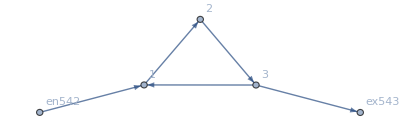

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j425→80/3,j426→80/3,j427→0,j428→80,j429→80,j430→0,j431→0,j432→160/3,j433→0,j434→0,jt435→0,jt436→0,jt437→0,jt438→0,jt439→80/3,jt440→160/3,jt441→80/3,jt442→0,jt443→0,jt444→80/3,jt445→0,jt446→160/3,jt447→0,jt448→0,u449→160/3,u450→80/3,u451→0,u452→0,u453→160/3,u454→80/3,u455→0,u456→160/3,u457→0,u458→160/3|>

#### Non-linear case

```mathematica
alpha = 0;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0179586

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0177279

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0174905

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0172467

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0169969

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0167415

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0164808

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0162152

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.015945

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0156705

<|j425→20.5557,j426→20.5557,j427→0,j428→80,j429→80,j430→0,j431→0,j432→59.4443,j433→0,j434→0,jt435→0,jt436→0,jt437→0,jt438→0,jt439→20.5557,jt440→59.4443,jt441→20.5557,jt442→0,jt443→0,jt444→20.5557,jt445→0,jt446→59.4443,jt447→0,jt448→0,u449→3.0523,u450→1.52615,u451→0.,u452→0,u453→3.0523,u454→1.52615,u455→0.,u456→3.0523,u457→0,u458→3.0523|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0201858

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0198039

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0194149

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0190197

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.018619

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0182136

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0178043

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0173918

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0169767

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0165597

<|j425→20.0153,j426→20.0153,j427→0,j428→80,j429→80,j430→0,j431→0,j432→59.9847,j433→0,j434→0,jt435→0,jt436→0,jt437→0,jt438→0,jt439→20.0153,jt440→59.9847,jt441→20.0153,jt442→0,jt443→0,jt444→20.0153,jt445→0,jt446→59.9847,jt447→0,jt448→0,u449→3.60266,u450→1.80133,u451→0.,u452→0,u453→3.60266,u454→1.80133,u455→0.,u456→3.60266,u457→0,u458→3.60266|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0259476

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0249064

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0238756

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0228586

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0218582

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0208768

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0199166

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0189794

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0180665

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0171791

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0163183

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0154846

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0146786

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0139006

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0131509

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0124294

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0117362

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0110711

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0104337

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.00982389

<|j425→14.1258,j426→14.1258,j427→0,j428→80,j429→80,j430→0,j431→0,j432→65.8742,j433→0,j434→0,jt435→0,jt436→0,jt437→0,jt438→0,jt439→14.1258,jt440→65.8742,jt441→14.1258,jt442→0,jt443→0,jt444→14.1258,jt445→0,jt446→65.8742,jt447→0,jt448→0,u449→5.12141,u450→2.5607,u451→0.,u452→0,u453→5.12141,u454→2.5607,u455→0.,u456→5.12141,u457→0,u458→5.12141|>

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0369234

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0166028

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.00746454

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.003356

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.00150885

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000678377

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000304999

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000137128

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0000616529

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0000277193

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0000124626

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.60323×10^-6

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.51922×10^-6

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.13265×10^-6

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.0924×10^-7

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.28955×10^-7

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.02939×10^-7

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.62815×10^-8

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.08082×10^-8

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 9.35543×10^-9

<|j425→24.5225,j426→24.5225,j427→0,j428→80,j429→80,j430→0,j431→0,j432→55.4775,j433→0,j434→0,jt435→0,jt436→0,jt437→0,jt438→0,jt439→24.5225,jt440→55.4775,jt441→24.5225,jt442→0,jt443→0,jt444→24.5225,jt445→0,jt446→55.4775,jt447→0,jt448→0,u449→33.0089,u450→16.5045,u451→0.,u452→0,u453→33.0089,u454→16.5045,u455→0.,u456→33.0089,u457→0,u458→33.0089|>

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[6.96187×10^-14,ComplexInfinity]

<|j425→80/3,j426→80/3,j427→0,j428→80,j429→80,j430→0,j431→0,j432→160/3,j433→0,j434→0,jt435→0,jt436→0,jt437→0,jt438→0,jt439→80/3,jt440→160/3,jt441→80/3,jt442→0,jt443→0,jt444→80/3,jt445→0,jt446→160/3,jt447→0,jt448→0,u449→160/3,u450→80/3,u451→0,u452→0,u453→160/3,u454→80/3,u455→0,u456→160/3,u457→0,u458→160/3|>

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],1,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.617897

<|j425→43.5865,j426→43.5865,j427→0,j428→80,j429→80,j430→0,j431→0,j432→36.4135,j433→0,j434→0,jt435→0,jt436→0,jt437→0,jt438→0,jt439→43.5865,jt440→36.4135,jt441→43.5865,jt442→0,jt443→0,jt444→43.5865,jt445→0,jt446→36.4135,jt447→0,jt448→0,u449→187.318,u450→93.659,u451→0.,u452→0,u453→187.318,u454→93.659,u455→0.,u456→187.318,u457→0,u458→187.318|>

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.00001

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

«6 more identical outputs»

<|j1279→0,j1280→0.,j1281→0,j1282→80.,j1283→80.,j1284→1.25521×10^189,j1285→1.25521×10^189,j1286→1.25521×10^189,j1287→0.,j1288→0.,jt1289→1.25521×10^189,jt1290→0.,jt1291→0.,jt1292→0.,jt1293→0.,jt1294→80.,jt1295→0.,jt1296→1.25521×10^189,jt1297→0.,jt1298→0.,jt1299→1.25521×10^189,jt1300→80.,jt1301→0.,jt1302→0.,u1303→0.,u1304→0.,u1305→15.,u1306→15.,u1307→0.,u1308→0.,u1309→15.,u1310→0.,u1311→15.,u1312→0.|>

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],4,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

«1 more identical outputs»

<|j425→0,j426→0,j427→0,j428→80,j429→80,j430→5.49218×10^296,j431→5.49218×10^296,j432→5.49218×10^296,j433→0,j434→0,jt435→5.49218×10^296,jt436→0,jt437→0,jt438→0,jt439→0,jt440→80,jt441→0,jt442→5.49218×10^296,jt443→0,jt444→0,jt445→5.49218×10^296,jt446→80,jt447→0,jt448→0,u449→0.,u450→0.,u451→0.,u452→0,u453→0.,u454→0.,u455→0.,u456→0.,u457→0,u458→0.|>

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

«7 more identical outputs»

<|j1279→0,j1280→0.,j1281→0,j1282→80.,j1283→80.,j1284→1.23536349271862×10^859,j1285→1.23536349271862×10^859,j1286→1.23536349271862×10^859,j1287→0.,j1288→0.,jt1289→1.23536349271862×10^859,jt1290→0.,jt1291→0.,jt1292→0.,jt1293→0.,jt1294→80.,jt1295→0.,jt1296→1.23536349271862×10^859,jt1297→0.,jt1298→0.,jt1299→1.23536349271862×10^859,jt1300→80.,jt1301→0.,jt1302→0.,u1303→0``-843.7392649841213,u1304→0``-843.4382349884572,u1305→15.,u1306→15.,u1307→0``-843.4382349884572,u1308→0``-843.4382349884572,u1309→15.,u1310→0``-843.4382349884572,u1311→15.,u1312→0.|>

$Aborted

$Aborted

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],8,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

«4 more identical outputs»

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1.,ComplexInfinity]

<|j425→80/3,j426→80/3,j427→0,j428→80,j429→80,j430→0,j431→0,j432→160/3,j433→0,j434→0,jt435→0,jt436→0,jt437→0,jt438→0,jt439→80/3,jt440→160/3,jt441→80/3,jt442→0,jt443→0,jt444→80/3,jt445→0,jt446→160/3,jt447→0,jt448→0,u449→160/3,u450→80/3,u451→0,u452→0,u453→160/3,u454→80/3,u455→0,u456→160/3,u457→0,u458→160/3|>